```mathematica
{{(*Define the size of the grid*)
gridSize=10;

(*Generate places and transitions using strings with commas in indices*)
places=Table["p"<>ToString[i]<>","<>ToString[j],{i,1,gridSize},{j,1,gridSize}];
transitions=Table["t"<>ToString[i]<>","<>ToString[j],{i,1,gridSize},{j,1,gridSize}];

(*Flatten places and transitions for use in arcs and visualization*)
flatPlaces=Flatten[places];
flatTransitions=Flatten[transitions];

(*Define the arcs*)
arcs=Flatten[Table[{
(*Horizontal connections*)
places[[i,j]]->transitions[[i,j]],transitions[[i,j]]->places[[i,j]],If[j<gridSize,places[[i,j]]->places[[i,j+1]],Nothing],If[j<gridSize,places[[i,j+1]]->places[[i,j]],Nothing],
(*Vertical connections*)
If[i<gridSize,places[[i,j]]->places[[i+1,j]],Nothing],If[i<gridSize,places[[i+1,j]]->places[[i,j]],Nothing]},{i,1,gridSize},{j,1,gridSize}]];

(*Define vertex coordinates for a grid layout*)
vertexCoordinates=Association[Join[
(*Place positions*)
Table[places[[i,j]]->{j,gridSize-i+1},{i,1,gridSize},{j,1,gridSize}],
(*Transition positions slightly offset from places*)
Table[transitions[[i,j]]->{j+0.3,gridSize-i+0.7},{i,1,gridSize},{j,1,gridSize}]]];

(*Visualize the Petri net with Graph*)
Graph[arcs,VertexCoordinates->vertexCoordinates,GraphStyle->"Detailed",ImageSize->Large,VertexLabels->"Name"]}, {□}}
```

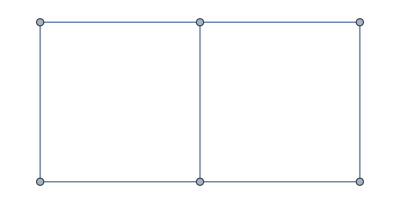

```mathematica
GraphProduct[PathGraph[{1,2}],PathGraph[{1,2,3}],GraphLayout->"GridEmbedding"]
```

```mathematica
(* Generate a CS2 hardware configuration *)
DirectedGraph[GridGraph[{5,5}]]
```

-Graphics-

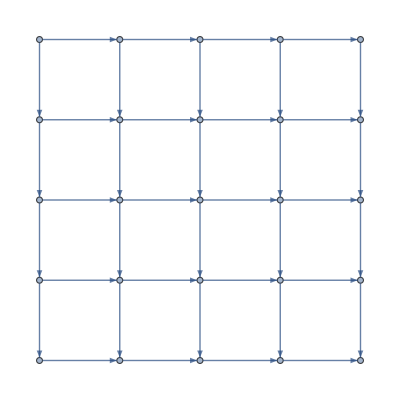

```mathematica
(* Generate a systolic matrix multiplication communication configuration *)
vertices=Flatten[Table[{i,j},{i,5},{j,5}],1];
edges=Join[Table[DirectedEdge[{i,j},{i+1,j}],{i,4},{j,5}],Table[DirectedEdge[{i,j},{i,j+1}],{i,5},{j,4}]  ];
Graph[vertices,Flatten[edges],DirectedEdges->True,VertexCoordinates->Association[Table[{i,j}->{j,-i},{i,5},{j,5}]//Flatten]]
```